# Convergent Test of Lagrange Inversion Series for Implied Volatility

## Black-Scholes Formulae

```mathematica
NormalCDF[d_]:=1/2(1+Erf[d/(√2)]);
LogForward[S_,K_,T_,r_,q_]:= Log[S/K]+(r-q)*T;
Std[σ_,T_]:= σ √T;
D1[lo_,Z_]:=lo/Z+Z/2;
D2[lo_,Z_]:=lo/Z-Z/2;
BSCallHandy[S_,K_,T_,r_,q_,σ_]:=S Exp[-q T]  NormalCDF[D1[LogForward[S,K,T,r,q],Std[σ,T]]]-K Exp[-r T]NormalCDF[D2[LogForward[S,K,T,r,q],Std[σ,T]]];
BSPutHandy[S_,K_,T_,r_,q_,σ_]:=-S Exp[-q T] NormalCDF[-D1[LogForward[S,K,T,r,q],Std[σ,T]]]+K Exp[-r T]NormalCDF[-D2[LogForward[S,K,T,r,q],Std[σ,T]]];
```

```mathematica
LISeries[S_,K_,T_,r_,q_,σ0_,N_] :=Module[{},
InverseSeries[Series[BSCallHandy[S,K,T,r,q,σ],{σ,σ0,N}]]];
```

```mathematica
N[BSCallHandy[100,100,1,0.05,0.01,0.3],10]
```

13.6164

```mathematica
LISeries[100,100,1,0.05,0.01,0.3,40]
```

0.3+0.0263551 (σ-13.6164)+5.4667×10^-6 (σ-13.6164)^2+2.57227×10^-6 (σ-13.6164)^3-1.56967×10^-7 (σ-13.6164)^4+1.43363×10^-8 (σ-13.6164)^5-1.28729×10^-9 (σ-13.6164)^6+1.16832×10^-10 (σ-13.6164)^7-1.06681×10^-11 (σ-13.6164)^8+9.80093×10^-13 (σ-13.6164)^9-9.05619×10^-14 (σ-13.6164)^10+8.41364×10^-15 (σ-13.6164)^11-7.85672×10^-16 (σ-13.6164)^12+7.37191×10^-17 (σ-13.6164)^13-6.94807×10^-18 (σ-13.6164)^14+6.57604×10^-19 (σ-13.6164)^15-6.24824×10^-20 (σ-13.6164)^16+5.95835×10^-21 (σ-13.6164)^17-5.70111×10^-22 (σ-13.6164)^18+5.47214×10^-23 (σ-13.6164)^19-5.26773×10^-24 (σ-13.6164)^20+5.08475×10^-25 (σ-13.6164)^21-4.92056×10^-26 (σ-13.6164)^22+4.77292×10^-27 (σ-13.6164)^23-4.6399×10^-28 (σ-13.6164)^24+4.51987×10^-29 (σ-13.6164)^25-4.4114×10^-30 (σ-13.6164)^26+4.31329×10^-31 (σ-13.6164)^27-4.22447×10^-32 (σ-13.6164)^28+4.14403×10^-33 (σ-13.6164)^29-4.07117×10^-34 (σ-13.6164)^30+4.00519×10^-35 (σ-13.6164)^31-3.94547×10^-36 (σ-13.6164)^32+3.89149×10^-37 (σ-13.6164)^33-3.84276×10^-38 (σ-13.6164)^34+3.79887×10^-39 (σ-13.6164)^35-3.75943×10^-40 (σ-13.6164)^36+3.72413×10^-41 (σ-13.6164)^37-3.69266×10^-42 (σ-13.6164)^38+3.66476×10^-43 (σ-13.6164)^39-3.6402×10^-44 (σ-13.6164)^40+O[σ-13.6164]^41

```mathematica
ACoeffs[S_,K_,T_,r_,q_,σ0_,N_] := Table[SeriesCoefficient[LISeries[S,K,T,r,q,σ0,N],n],{n,1,N}];
An[S_,K_,T_,r_,q_,σ0_,N_,n_] := SeriesCoefficient[LISeries[S,K,T,r,q,σ0,N],n];
Ln[S_,K_,T_,r_,q_,σ0_,N_,n_] := Abs[An[S,K,T,r,q,σ0,N,n]]^(-1/n)
```

```mathematica
An[100,100,1,0.05,0,0.3,30,30]
```

-1.54387×10^-33

```mathematica
ACoeffs[100,100,1,0.05,0.01,0.5,30]
```

{0.026735,0.0000400981,1.121×10^-6,-7.43454×10^-9,7.20067×10^-10,-3.38911×10^-11,1.83946×10^-12,-9.75665×10^-14,5.21734×10^-15,-2.79373×10^-16,1.49992×10^-17,-8.07144×10^-19,4.35338×10^-20,-2.35322×10^-21,1.27476×10^-22,-6.91985×10^-24,3.76386×10^-25,-2.0512×10^-26,1.11993×10^-27,-6.12563×10^-29,3.35627×10^-30,-1.84196×10^-31,1.01249×10^-32,-5.57396×10^-34,3.07304×10^-35,-1.69659×10^-36,9.37924×10^-38,-5.19174×10^-39,2.87733×10^-40,-1.59653×10^-41}

```mathematica
PlotL[S_,K_,T_,r_,q_,σ0_,N_]:=Module[{ln},
ln = Abs[ACoeffs[S,K,T,r,q,σ0,N]]^Table[-1/n,{n,1,N}];
Show[ListPlot[ln],GridLines -> {None, {ln[[N]] - 3*(ln[[N-5]]-ln[[N]])}},GridLinesStyle -> Directive[Dashed,Red],AxesLabel -> {"n","R_n"}]
]
```

```mathematica
Ln[100,60,1,0.05,0,1,30,30]
```

15.8693

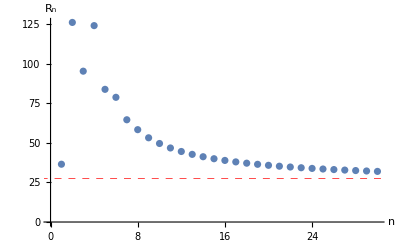

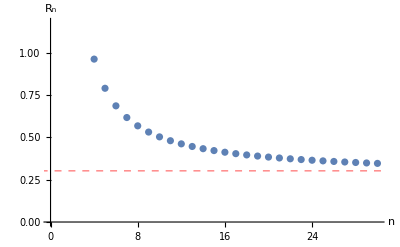

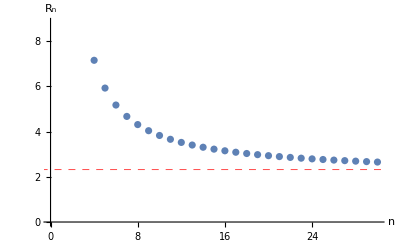

```mathematica
PlotL[100,100,1,0.05,0,0.7,30]
PlotL[100,60,1,0.05,0,0.3,30]
PlotL[100,150,1,0.05,0,0.3,30]
```

```mathematica
Ln[100,60,1,0.05,0,0.3,30,30]
```

0.346478

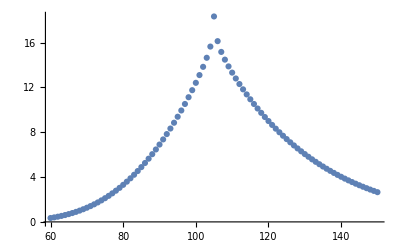

```mathematica
ListPlot[Table[{K,Ln[100,K,1,0.05,0,0.3,30,30] },{K,60,150,1}]]
```

### Tehranchi’s upper bound

```mathematica
TehUpperBound[C_,S_,K_,T_,r_,q_]:=Module[{c,k},
c=C/(S Exp[q T]);
k = Log[K/(S Exp[(r-q)T])];
-2 InverseCDF[NormalDistribution[0,1],(1-c)/(1+Exp[k])]/(√T)];
```

```mathematica
TehGivenSigma[S_,K_,T_,r_,q_,σ_]:=TehUpperBound[BSCallHandy[S,K,T,r,q,σ],S,K,T,r,q];
```

```mathematica
TehGivenSigma[100,100,1,0.05,0,0.3]
```

0.304157

```mathematica
PriceErrorTeh[S_,K_,T_,r_,q_,σ_]:=Abs[BSCallHandy[S,K,T,r,q,σ]-BSCallHandy[S,K,T,r,q,TehGivenSigma[S,K,T,r,q,σ]]]
```

```mathematica
PriceErrorTeh[100,60,1,0.05,0,0.3]
PriceErrorTeh[100,100,1,0.05,0,0.3]
PriceErrorTeh[100,150,1,0.05,0,0.3]
```

6.01803

0.157721

5.75035

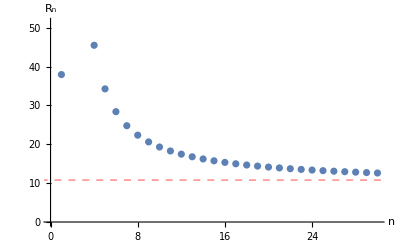

```mathematica
Module[{S=100,K=100,T=1,r=0.05,q=0,σ=0.3,σ0,N=30},
σ0 = TehGivenSigma[S,K,T,r,q,σ];
PlotL[S,K,T,r,q,σ0,N]]
```

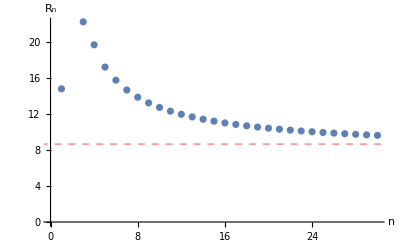

```mathematica
Module[{S=100,K=40,T=1,r=0.05,q=0,σ=0.3,σ0,N=30},
σ0 = TehGivenSigma[S,K,T,r,q,σ];
PlotL[S,K,T,r,q,σ0,N]]
```

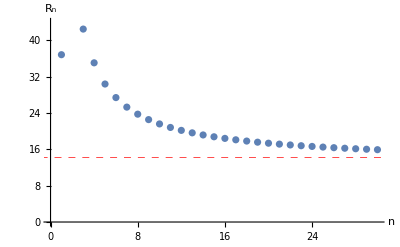

```mathematica
Module[{S=100,K=200,T=1,r=0.05,q=0,σ=0.3,σ0,N=30},
σ0 = TehGivenSigma[S,K,T,r,q,σ];
PlotL[S,K,T,r,q,σ0,N]]
```

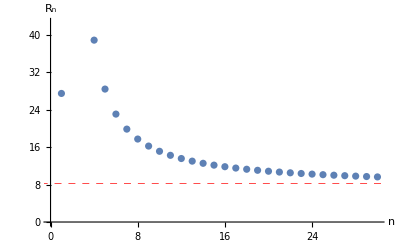

```mathematica
Module[{S=100,K=100,T=0.5,r=0.05,q=0,σ=0.3,σ0,N=30},
σ0 = TehGivenSigma[S,K,T,r,q,σ];
PlotL[S,K,T,r,q,σ0,N]]
```

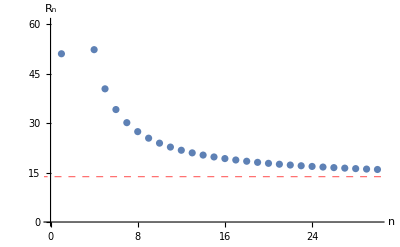

```mathematica
Module[{S=100,K=100,T=2,r=0.05,q=0,σ=0.3,σ0,N=30},
σ0 = TehGivenSigma[S,K,T,r,q,σ];
PlotL[S,K,T,r,q,σ0,N]]
```

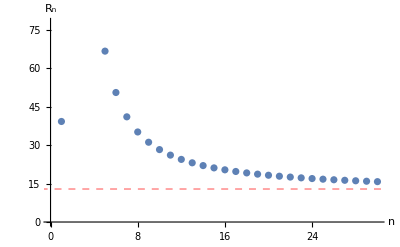

```mathematica
Module[{S=100,K=100,T=1,r=0.01,q=0,σ=0.3,σ0,N=30},
σ0 = TehGivenSigma[S,K,T,r,q,σ];
PlotL[S,K,T,r,q,σ0,N]]
```

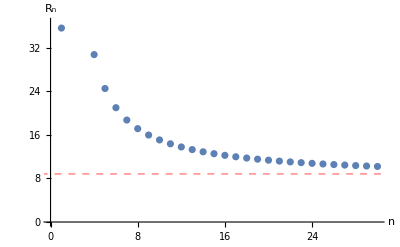

```mathematica
Module[{S=100,K=100,T=1,r=0.1,q=0,σ=0.3,σ0,N=30},
σ0 = TehGivenSigma[S,K,T,r,q,σ];
PlotL[S,K,T,r,q,σ0,N]]
```

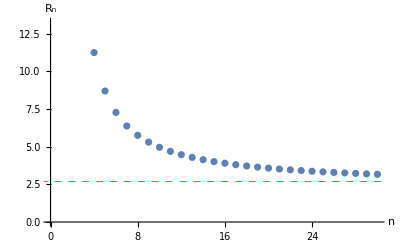

```mathematica
Module[{S=100,K=100,T=1,r=0.05,q=0,σ=0.1,σ0,N=30},
σ0 = TehGivenSigma[S,K,T,r,q,σ];
PlotL[S,K,T,r,q,σ0,N]]
```

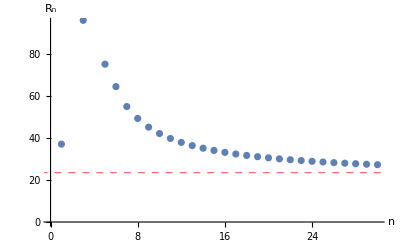

```mathematica
Module[{S=100,K=100,T=1,r=0.05,q=0,σ=0.6,σ0,N=30},
σ0 = TehGivenSigma[S,K,T,r,q,σ];
PlotL[S,K,T,r,q,σ0,N]]
```

```mathematica
Module[{S=100,K=200,T=1,r=0.05,q=0,σ=0.3,σ0,N=30},
σ0 = TehGivenSigma[S,K,T,r,q,σ];
PlotL[S,K,T,r,q,σ0,N]]
```

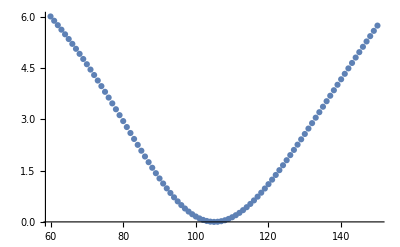

```mathematica
ListPlot[Table[{K,PriceErrorTeh[100,K,1,0.05,0,0.3]},{K,60,150,1}]]
```

```mathematica
Ln[100,60,1,0.05,0,0.3,30,30]
```

0.346478

```mathematica
ConvergenceAnalysis[S_,T_,r_,q_,σ_,Kmin_,Kmax_,step_]:=Module[{ln,priceDeviationTehn,fLn,fPriceDeviationTehn, pts, listPlot,plot},
ln = Table[{K,Ln[S,K,T,r,q,TehGivenSigma[S,K,T,r,q,σ],30,30] },{K,Kmin,Kmax,step}];
priceDeviationTehn = Table[{K,Abs[BSCallHandy[S,K,T,r,q,σ]-BSCallHandy[S,K,T,r,q,TehGivenSigma[S,K,T,r,q,σ]]]},{K,Kmin,Kmax,step}];
fLn = Interpolation[ln];
fPriceDeviationTehn = Interpolation[priceDeviationTehn];
(*pts = NSolve[fLn[K]==fPriceDeviationTehn[K],K];*)
listPlot = ListPlot[{ln,priceDeviationTehn},PlotMarkers->Automatic,PlotLegends->{"convergent radius","deviation"}];
plot = Plot[{fLn[K],fPriceDeviationTehn[K]},{K,Kmin,Kmax}];
Show[{listPlot,plot(*,Graphics[{Red,PointSize[Medium],Point[{x,y}/.pts]}]*)},AxesLabel -> {"strike",None}]
]
```

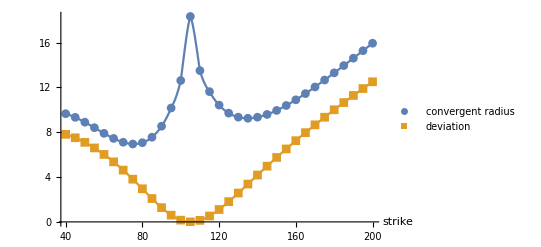

```mathematica
ConvergenceAnalysis[100,1,0.05,0,0.3,40,200,5]
```

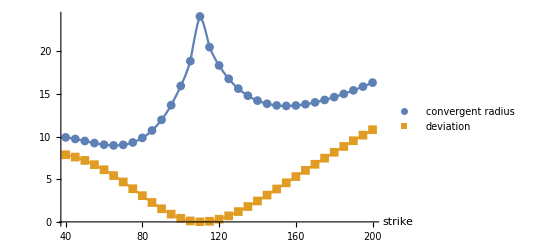

```mathematica
ConvergenceAnalysis[100,2,0.05,0,0.3,40,200,5]
```

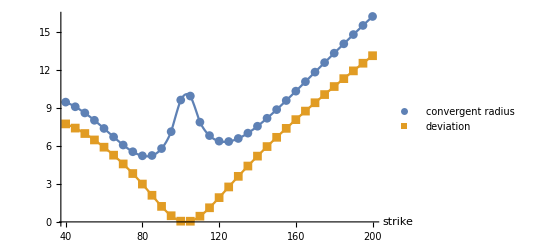

```mathematica
ConvergenceAnalysis[100,0.5,0.05,0,0.3,40,200,5]
```

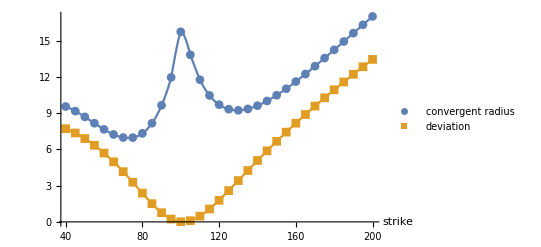

```mathematica
ConvergenceAnalysis[100,1,0.01,0,0.3,40,200,5]
```

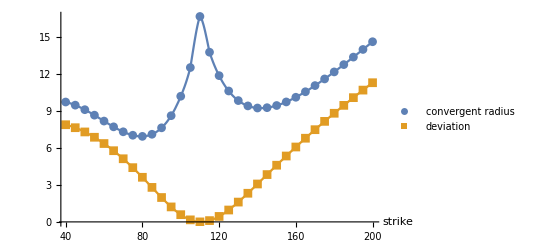

```mathematica
ConvergenceAnalysis[100,1,0.1,0,0.3,40,200,5]
```

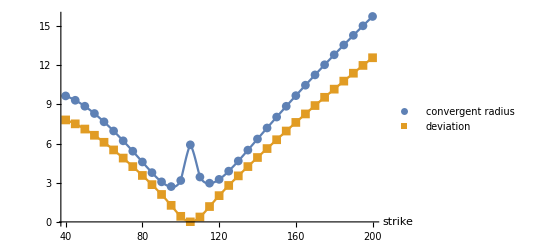

```mathematica
ConvergenceAnalysis[100,1,0.05,0,0.1,40,200,5]
```

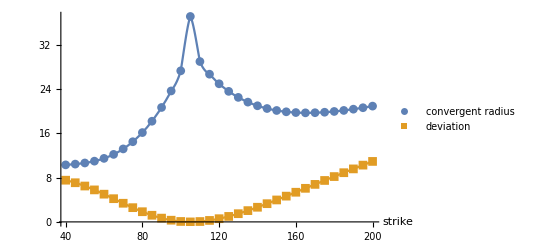

```mathematica
ConvergenceAnalysis[100,1,0.05,0,0.6,40,200,5]
```